# Predict the Scale of Satellite Images

Some explanation

Mehmet Sahin, Jun. 26,  2018

Some explanation

## Collect Satellite Images

In this section, we will get the data using GeoImage.

Some explanation

```mathematica
(*ClearAll["Global`*"]*)
```

Create a function to get countries’ geo positions randomly:

```mathematica
geoPositionOfCountry[entities_,numberOfPosition_Integer,folderName_String] :=
	Module[{},
	countries = entities;
	mesh = DiscretizeGraphics@EntityValue[countries,"Polygon"];
	SeedRandom[Hash@{folderName,countries}];
	Reverse[RandomPoint[mesh,numberOfPosition],{2}]
]
```

Let’s plot them and see how those random positions act on a Graphic

```mathematica
data = geoPositionOfCountry[{Entity["Country","Germany"],Entity["Country","Switzerland"],Entity["Country","Italy"],Entity["Country","Austria"],Entity["Country","Luxembourg"],Entity["Country","Belgium"],Entity["Country","Netherlands"]},10,"training"];
GeoListPlot@GeoPosition@data
```

-Graphics-

```mathematica
getZoomLevel[point_] := 
	(SeedRandom[Hash[point]]; normalize[RandomReal[]]);
```

```mathematica
SetAttributes[{getGeoRange, normalize}, Listable]

(*getGeoRange[zoom_] := zoom * Quantity[8800,"Miles"] + Quantity[0.2,"Miles"];*)
getGeoRange[zoom_] := zoom * 8800 + 0.2;
normalize[number_] := If[number<0.3,number,number^17];
(*ImagePartition[GeoImage[Entity["Country","Italy"], GeoRange->getGeoRange[1],ImageSize->800],{100}] // Grid;*)
```

```mathematica
zoomLevel = getZoomLevel[#]&/@data;
geoRange = getGeoRange@getZoomLevel[#]&/@data;
```

Check the distribution of points and zoom level:

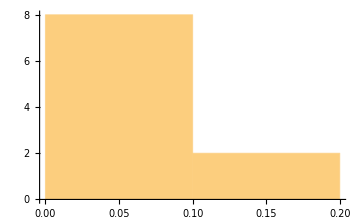

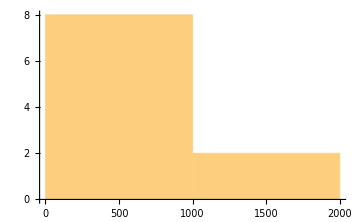

1631.87

-Graphics-

0.200169

GeoServer::mlim: You have reached your monthly limit for high-resolution geo imagery. To request information on extending it, contact us at https://wolfr.am/mNYboAZD.

GeoImage::wdata: Unable to download data for ranges {{41.8871,41.8929},{12.4961,12.5039}} and zoom level 16 from the Wolfram geo server.

GeoImage[{Rome},Automatic,GeoRange→0.200169 mi,ImageSize→Medium]

```mathematica
Histogram@zoomLevel
Histogram@geoRange
Max[geoRange]
GeoImage[Entity["City",{"Rome","Lazio","Italy"}],GeoRange->Quantity[Max[geoRange],"Miles"],ImageSize->Medium]
minGeoRange =Min[geoRange]
GeoImage[Entity["City",{"Rome","Lazio","Italy"}],GeoRange->Quantity[minGeoRange,"Miles"],ImageSize->Medium]
```

Create a function to return a association of points and zoom level:

```mathematica
associateThePositionsWithGeoRange[points_List] := 
	Map[<|"Point"->#,"Zoom"->getZoomLevel[#]|>&,points];
```

Call the createTheDataSet function:

```mathematica
assocoatedData = associateThePositionsWithGeoRange[data];
```

```mathematica
Length@assocoatedData
Take[assocoatedData,2]
Take[Dataset@assocoatedData,2]
```

1000

{<|Point→{45.9551,8.56637},Zoom→1.73191×10^-7|>,<|Point→{48.3537,14.9246},Zoom→0.0219984|>}

Dataset[<>]

Let’s now write our function that will encode and decode name of the images:

```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

Try out the encodeID and decodeID:

```mathematica
Part[assocoatedData,2]
encodeID[Part[assocoatedData,2]]
decodeID[%]
```

<|Point→{48.3537,14.9246},Zoom→0.0219984|>

ODpBAi1TBVBvaW50wSMBAqhwUEZHLUhANWgP5GPZLUAtUwRab29tco6K8PDAhpY~

<|Point→{48.3537,14.9246},Zoom→0.0219984|>

### So, far we have created all the needed functions. Now, we will create our new function that takes all the function and creates folder for a image with association name which was encoded. Then, we will part our image into sub images and store them into the folder we created. This will continue for every image we get using GeoImage.

Create a function to getImages from GeoImage:

```mathematica
getImage[coords_List, range_] := 
  	GeoImage[GeoPosition[coords], GeoRange ->range];
```

Before we create our store image function, we should create a hash function to get unique names for images:

```mathematica
(*hash[expr_] := 
	IntegerString[Hash[expr],36];*)
```

Now, let’s create our storeImage function:

```mathematica
ClearAll[imageLocation]
(*imageLocation[zoomLevel_,imageNumber_] := 
	FileNameJoin[{NotebookDirectory[],ToString[zoomLevel]<>"-"<>ToString[imageNumber]<>".png"}];*)
imageLocation[notebookDirectory_,zoomLevel_,imageNumber_] := 
	FileNameJoin[{notebookDirectory,encodeID[ToString[zoomLevel]<>"-"<>ToString[imageNumber]]<>".png"}];
```

Create a function to get folder location with encoded name:

```mathematica
ClearAll[folderLocation]
folderLocation[exp_,trainingOrTestingFolder_] := 
	FileNameJoin[{NotebookDirectory[],"StalliteImages",trainingOrTestingFolder,encodeID[exp]}];
```

### Okey now it is time to create our function to partition images into smaller parts.

```mathematica
(*When images were parted, their zoom level changed. To prevent that, I also converted the zoom leve for each image by simply dividing the real zoom level with the number of images!*)
partitionTheImage[img_,geoRange_,levelOfPartition_] := 
	Table[<|geoRange/n->Flatten@ImagePartition[img,Scaled[1/n]]|>,{n,1,levelOfPartition}];

saveImages[folderName_,partedImage_] :=
	Table[
		Module[{key,values,imglocation},
		key = First[Keys@partedImage];
		values = Flatten@Values[partedImage];
		imglocation = imageLocation[folderName,key,count];
		If[FileExistsQ@imglocation,Missing["ImgAlreadyExist"],Export[imglocation,ImageResize[Part[values,count],40]]]
	],{count, 1, Length@Flatten@Values[partedImage]}]
```

### Time has come, Lets add all the functions:

```mathematica
ClearAll[folderName,imgPosition,geoRangeZoom,img,imglocation];
createTheDataSet[assoPointAndGeoRange_Association,trainingOrTestingFolder_String,levelOfPartition_] := 
	Module[{folderName,geoPosition,geoRangeZoom,img,partedImage,imglocation},
		folderName = folderLocation[assoPointAndGeoRange,trainingOrTestingFolder];
		If[FileExistsQ@folderName,(*Throw[Missing["FolderAlreadyExist"]]*),CreateDirectory@folderName];
		geoPosition = assoPointAndGeoRange["Point"];
		geoRangeZoom = getGeoRange@assoPointAndGeoRange["Zoom"];
		img = getImage[geoPosition,Quantity[geoRangeZoom,"Miles"]];
		If[
			ImageQ@img,
			partedImage = partitionTheImage[img, geoRangeZoom,levelOfPartition];
			saveImages[folderName,#]&/@partedImage
		]
	]
```

```mathematica
(*ParallelMap[createTheDataSet[#,"Training",5]&,assocoatedData];*)
```

## Create the Network

In the last section, we collected the satellite images using GeoImage and store all those images on our hard drive. In this section, we will create our Neural Network so we can feed it with the data we have.

## Test the Network

Now ..

## Conclusion

## Author contact information

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com

## Further Work

Mehmet Sahin

6/28/2018
mehmetmshin@gmail.com